# Thermal Conductivity by numeric integration

```mathematica
SetDirectory[]
SetDirectory["Documents/Wolfram Mathematica/Antiferromagnet/"]
Directory[]
```

/home/bkoehler

/home/bkoehler/Documents/Wolfram Mathematica/Antiferromagnet

/home/bkoehler/Documents/Wolfram Mathematica/Antiferromagnet

## Plot

```mathematica
J=1;
γ[kx_,ky_]:=1/2*(Cos[kx]+Cos[ky]);
A[kx_,ky_,b_]:=1+γ[kx,ky]*b^2;
B[kx_,ky_,b_]:=γ[kx,ky]*(1-b^2);
ϵ[kx_,ky_,b_]:=2*J*Sqrt[A[kx,ky,b]^ 2-B[kx,ky,b]^ 2];
heatconductivitydensity[kx_,ky_,b_,β_,τ_]:=-( J^2 (-2*b^2-2*γ[kx,ky]*(2*b^2-1)))^2*(Sin[kx]^2+Sin[ky]^2)*(β^2/2)/(1-Cosh[β*ϵ[kx,ky,b]])*τ;
FullSimplify[MatrixForm[(D[ϵ[kx,ky,b],{{kx,ky}}]*ϵ[kx,ky,b])]]
```

((-2 b^2+Cos[kx]-2 b^2 Cos[kx]+Cos[ky]-2 b^2 Cos[ky]) Sin[kx]
(-2 b^2+Cos[kx]-2 b^2 Cos[kx]+Cos[ky]-2 b^2 Cos[ky]) Sin[ky])

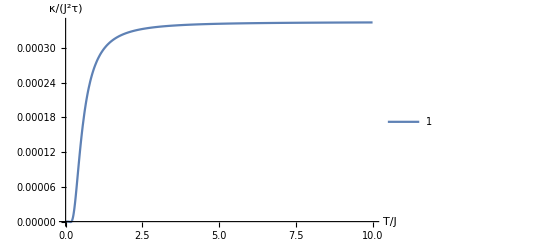

```mathematica
Plot[{1/(4π^2)*NIntegrate[heatconductivitydensity[kx,ky,0.45,1/T,1],{kx,-π,π},{ky,-π,π},MaxRecursion->100000,MinRecursion->90000,AccuracyGoal->100]-1/(4π^2)*NIntegrate[heatconductivitydensity[kx,ky,0.46,1/T,1],{kx,-π,π},{ky,-π,π},MaxRecursion->100000,MinRecursion->90000,AccuracyGoal->100]},{T,0.001,10},AxesOrigin->{0,0},PlotRange->All,AxesLabel->{Style["T/J",18],Style["κ/(J^2τ)",18]},PlotLegends->True]
```

```mathematica
Length[Blist]
```

300

{{0.464,9.32507},{0.4641,9.32506},{0.4642,9.32505},{0.4643,9.32504},{0.4644,9.32504},{0.4645,9.32503},{0.4646,9.32503},{0.4647,9.32503},{0.4648,9.32503},{0.4649,9.32503},{0.465,9.32504},{0.4651,9.32504},{0.4652,9.32505},{0.4653,9.32505},{0.4654,9.32506},{0.4655,9.32507},{0.4656,9.32508},{0.4657,9.3251},{0.4658,9.32511},{0.4659,9.32513},{0.466,9.32514}}

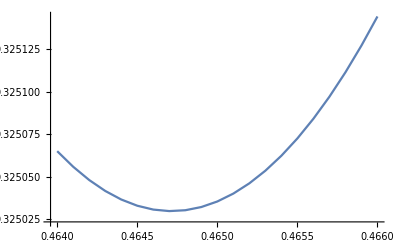

{{0.4647,9.32503}}

```mathematica
aaaaNiklas=Table[{b,NIntegrate[heatconductivitydensity[kx,ky,b,1./3.,1],{kx,-π,π},{ky,-π,π},MaxRecursion->100000,MinRecursion->90000,AccuracyGoal->100]},{b,0.464,0.466,0.0001}]
ListLinePlot[aaaaNiklas]
MinimalBy[aaaaNiklas,Last]
```

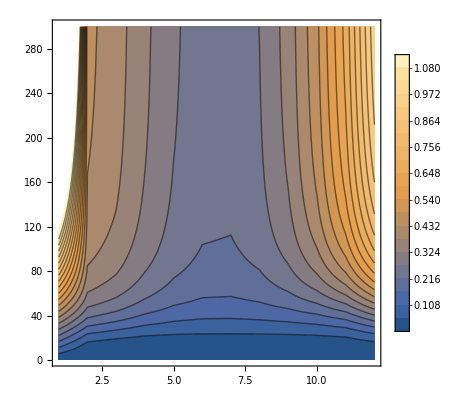

```mathematica
ListContourPlot[Blist,PlotLegends->Automatic,Contours->20]
```

```mathematica
NSolve[b^2/(Sqrt[1-b^ 2])==b,b]
```

{{b→0.707107},{b→0.}}

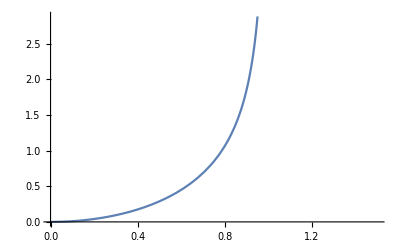

```mathematica
Plot[b^2/(Sqrt[1-b^ 2]),{b,0,1.5}]
```

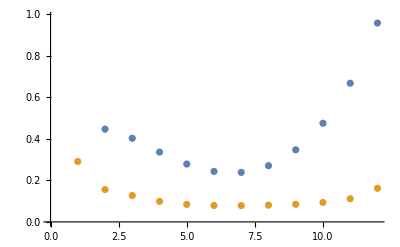

```mathematica
ListPlot[{Last[Blist],Blist[[30]]}]
```

```mathematica
Blist=Table[Flatten[{T,Table[1/(4π^2)*NIntegrate[heatconductivitydensity[kx,ky,b,1/T,1],{kx,-π,π},{ky,-π,π},MaxRecursion->100000,MinRecursion->90000,AccuracyGoal->100],{b,0,1,0.1}],1/(4π^2)*NIntegrate[heatconductivitydensity[kx,ky,0.48,1/T,1],{kx,-π,π},{ky,-π,π},MaxRecursion->100000,MinRecursion->90000,AccuracyGoal->100]},1],{T,0.001,3,0.01}];
```

```mathematica
Export["/home/bkoehler/Documents/Wolfram Mathematica/Antiferromagnet/fancyplot/BfieldtauconstTdep.dat",Blist,"Data"]
```

/home/bkoehler/Documents/Wolfram Mathematica/Antiferromagnet/fancyplot/BfieldtauconstTdep.dat

## Plot for different fields

```mathematica
plotlist=ParallelTable[Table[{T,NIntegrate[heatconductivitydensity[kx,ky,b,1/T,1],{kx,-π,π},{ky,-π,π},MaxRecursion->100000,MinRecursion->90000,AccuracyGoal->64]},{T,0.001,1,0.001}],{b,0,1,0.1}];
```

Get::noopen: Cannot open CloudObjectLoader`.

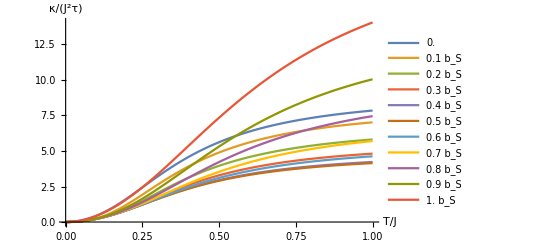

```mathematica
ListPlot[plotlist,Joined->True,PlotLegends->Table["b_S" N[i],{i,0,1,1/(Length[plotlist]-1)}],AxesLabel->{Style["T/J",18],Style["κ/(J^2τ)",18]}]
```

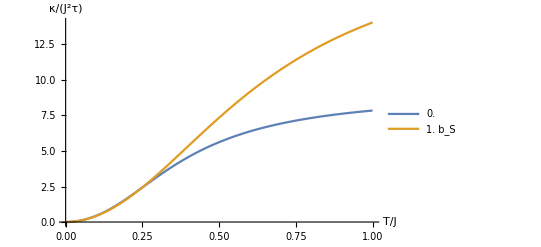

```mathematica
ListPlot[{plotlist[[1]],plotlist[[11]]},Joined->True,PlotLegends->Table["b_S" N[i],{i,0,1}],AxesLabel->{Style["T/J",18],Style["κ/(J^2τ)",18]}]
```

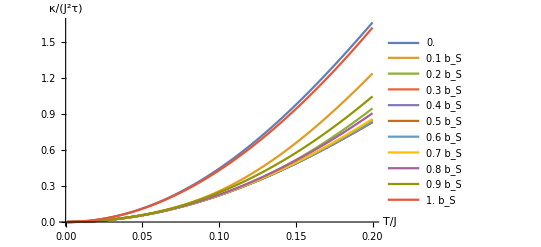

```mathematica
ListPlot[Table[Table[plotlist[[i]][[j]],{j,1,200}],{i,1,Length[plotlist]}],Joined->True,PlotLegends->Table["b_S" N[i],{i,0,1,1/(Length[plotlist]-1)}],AxesLabel->{Style["T/J",18],Style["κ/(J^2τ)",18]}]
```

```mathematica
plotlist2=ParallelTable[Table[{T,NIntegrate[heatconductivitydensity[kx,ky,b,1/T,1],{kx,-π,π},{ky,-π,π},MaxRecursion->100000,MinRecursion->90000,AccuracyGoal->64]},{T,0.001,0.2,0.001}],{b,0.99,1,0.002}];
```

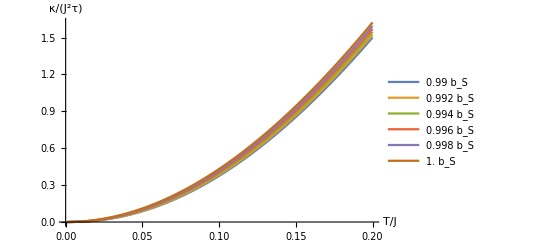

```mathematica
ListPlot[plotlist2[[1;;Length[plotlist2]]],PlotLegends->Table["b_S" N[i*0.01+0.99],{i,0,1,1/(Length[plotlist2]-1)}],Joined->True,AxesLabel->{Style["T/J",18],Style["κ/(J^2τ)",18]}]
```

```mathematica
plotlist3=ParallelTable[Table[{T,NIntegrate[heatconductivitydensity[kx,ky,b,1/T,1],{kx,-π,π},{ky,-π,π},MaxRecursion->100000,MinRecursion->90000,AccuracyGoal->64]},{T,1/1000,2/10,1/1000}],{b,0,2/10,2/100}];
```

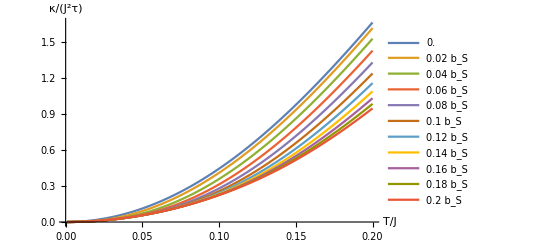

```mathematica
ListPlot[plotlist3[[1;;Length[plotlist3]]],PlotLegends->Table["b_S" N[i*0.1],{i,0,2,2/(Length[plotlist3]-1)}],Joined->True,AxesLabel->{Style["T/J",18],Style["κ/(J^2τ)",18]}]
```

## Thermal Conductivity for narrowed Brillouin zone

```mathematica
ϵ[0,0,1]
```

4

center

```mathematica
Δ=π/10;
blowend=0.3;
bhighend=1.0;
narrowedtocentersmallfield=ParallelTable[Table[{T,NIntegrate[heatconductivitydensity[kx,ky,b,1/T,1],{kx,-Δ,Δ},{ky,-Δ,Δ},MaxRecursion->100000,MinRecursion->90000,AccuracyGoal->100]/NIntegrate[heatconductivitydensity[kx,ky,b,1/T,1],{kx,-π,π},{ky,-π,π},MaxRecursion->100000,MinRecursion->90000,AccuracyGoal->100]},{T,0.001,0.3,0.005}],{b,0,blowend,0.05}];
narrowedtocenterlargefield=ParallelTable[Table[{T,NIntegrate[heatconductivitydensity[kx,ky,b,1/T,1],{kx,-Δ,Δ},{ky,-Δ,Δ},MaxRecursion->100000,MinRecursion->90000,AccuracyGoal->100]/NIntegrate[heatconductivitydensity[kx,ky,b,1/T,1],{kx,-π,π},{ky,-π,π},MaxRecursion->100000,MinRecursion->90000,AccuracyGoal->100]},{T,0.001,1,0.005}],{b,blowend,bhighend,0.1}];
```

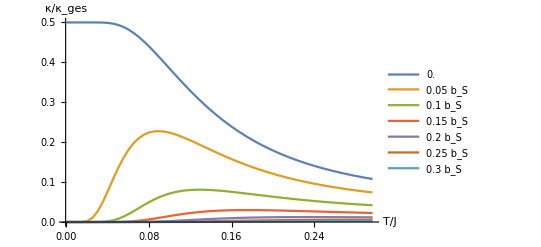

```mathematica
ListPlot[narrowedtocentersmallfield,PlotLegends->Table["b_S" N[blowend*i],{i,0,1,1/(Length[narrowedtocentersmallfield]-1)}],Joined->True,AxesLabel->{Style["T/J",18],Style["κ/κ_ges",18]},PlotRange->All]
```

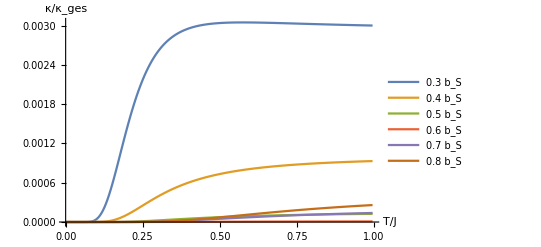

```mathematica
ListPlot[narrowedtocenterlargefield,PlotLegends->Table["b_S" N[i*(bhighend-blowend)+blowend],{i,0,1,1/(Length[narrowedtocenterlargefield]-1)}],Joined->True,AxesLabel->{Style["T/J",18],Style["κ/κ_ges",18]},PlotRange->All]
```

```mathematica
Δ=π/10;
blowend=0.3;
bhighend=1.0;
```

```mathematica
Δ=π/10;
blowend=0.3;
bhighend=1.0;
centerkappa1=Table[Flatten[{T,Table[NIntegrate[heatconductivitydensity[kx,ky,b,1/T,1],{kx,-Δ,Δ},{ky,-Δ,Δ},MaxRecursion->100000,MinRecursion->90000,AccuracyGoal->100]/NIntegrate[heatconductivitydensity[kx,ky,b,1/T,1],{kx,-π,π},{ky,-π,π},MaxRecursion->100000,MinRecursion->90000,AccuracyGoal->100],{b,0,blowend,0.05}]},1],{T,0.001,0.6,0.005}];
Export["/home/bkoehler/Documents/Wolfram Mathematica/Antiferromagnet/fancyplot/kappacentertauconstlowB.dat",centerkappa1,"Data"];
centerkappa2=Table[Flatten[{T,Table[NIntegrate[heatconductivitydensity[kx,ky,b,1/T,1],{kx,-Δ,Δ},{ky,-Δ,Δ},MaxRecursion->100000,MinRecursion->90000,AccuracyGoal->100]/NIntegrate[heatconductivitydensity[kx,ky,b,1/T,1],{kx,-π,π},{ky,-π,π},MaxRecursion->100000,MinRecursion->90000,AccuracyGoal->100],{b,blowend,bhighend,0.05}]},1],{T,0.001,3,0.02}];
Export["/home/bkoehler/Documents/Wolfram Mathematica/Antiferromagnet/fancyplot/kappacentertauconsthighB.dat",centerkappa2,"Data"];
```

## behaviour of the heat conductivity’s density in the vicinity of the center

```mathematica
Manipulate[Plot[{(-(4^2/T^2*(3b^2-1)^2)/(1-1*Cosh[4*b/T])*x^2),heatconductivitydensity[x,x,b,1/T,1]},{x,0,0.01},PlotRange->All],{T,0.001,1},{b,0.01,1}]
```

```mathematica
Series[4*J*s*Sqrt[(1/4*x^2)*(1-(-1+x^2/4)*(1-2b^2))],{x,0,3}]
```

2 √(2-2 b^2) s x+((-1+2 b^2) s x^3)/(4 √2 √(1-b^2))+O[x]^4

edges

```mathematica
narrowedtoedgessmallfield=ParallelTable[Table[{T,4*NIntegrate[heatconductivitydensity[kx,ky,b,1/T,1],{kx,-π,-π+Δ},{ky,-π,-π+Δ},MaxRecursion->100000,MinRecursion->90000,AccuracyGoal->100]/NIntegrate[heatconductivitydensity[kx,ky,b,1/T,1],{kx,-π,π},{ky,-π,π},MaxRecursion->100000,MinRecursion->90000,AccuracyGoal->100]},{T,0.001,0.3,0.005}],{b,0,0.1,0.01}];
narrowedtoedgeslargefield=ParallelTable[Table[{T,4*NIntegrate[heatconductivitydensity[kx,ky,b,1/T,1],{kx,-π,-π+Δ},{ky,-π,-π+Δ},MaxRecursion->100000,MinRecursion->90000,AccuracyGoal->100]/NIntegrate[heatconductivitydensity[kx,ky,b,1/T,1],{kx,-π,π},{ky,-π,π},MaxRecursion->100000,MinRecursion->90000,AccuracyGoal->100]},{T,0.001,0.3,0.005}],{b,0.9,1,0.01}];
```

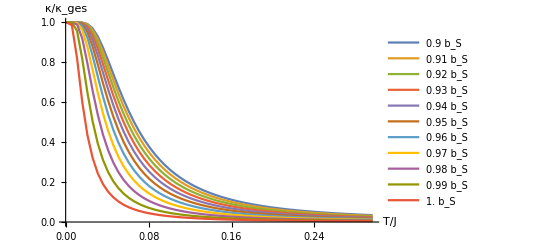

```mathematica
ListPlot[narrowedtoedgeslargefield,PlotLegends->Table["b_S" N[i+0.9],{i,0,1,0.1/(Length[narrowedtoedgeslargefield]-1)}],Joined->True,AxesLabel->{Style["T/J",18],Style["κ/κ_ges",18]},PlotRange->All]
```

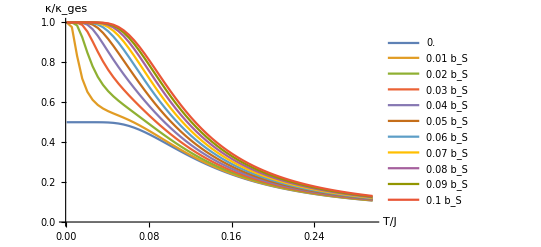

```mathematica
ListPlot[narrowedtoedgessmallfield,PlotLegends->Table["b_S" N[i],{i,0,1,0.1/(Length[narrowedtoedgessmallfield]-1)}],Joined->True,AxesLabel->{Style["T/J",18],Style["κ/κ_ges",18]},PlotRange->All]
```

```mathematica
Δ=π/10;
blowend=0.3;
bhighend=1.0;
edgekappa1=Table[Flatten[{T,Table[4*NIntegrate[heatconductivitydensity[kx,ky,b,1/T,1],{kx,-π,-π+Δ},{ky,-π,-π+Δ},MaxRecursion->100000,MinRecursion->90000,AccuracyGoal->100]/NIntegrate[heatconductivitydensity[kx,ky,b,1/T,1],{kx,-π,π},{ky,-π,π},MaxRecursion->100000,MinRecursion->90000,AccuracyGoal->100],{b,0,blowend,0.05}]},1],{T,0.001,0.6,0.005}];
Export["/home/bkoehler/Documents/Wolfram Mathematica/Antiferromagnet/fancyplot/kappaedgetauconstlowB.dat",edgekappa1,"Data"];
edgekappa2=Table[Flatten[{T,Table[4*NIntegrate[heatconductivitydensity[kx,ky,b,1/T,1],{kx,-π,-π+Δ},{ky,-π,-π+Δ},MaxRecursion->100000,MinRecursion->90000,AccuracyGoal->100]/NIntegrate[heatconductivitydensity[kx,ky,b,1/T,1],{kx,-π,π},{ky,-π,π},MaxRecursion->100000,MinRecursion->90000,AccuracyGoal->100],{b,blowend,bhighend,0.05}]},1],{T,0.001,0.6,0.005}];
Export["/home/bkoehler/Documents/Wolfram Mathematica/Antiferromagnet/fancyplot/kappaedgetauconsthighB.dat",edgekappa2,"Data"];
```

## behaviour of the heat conductivity’s density in the vicinity of the edges

```mathematica
Manipulate[Plot[{(Sqrt[2])^2/2*((1-b^2)-3/8*(1-2b^2)*(x-Pi)^2),heatconductivitydensity[x,x,b,1/T,1]},{x,Pi-0.25,Pi},PlotRange->All],{T,0.001,1},{b,0,1}]
```

(π/2,π/2)

```mathematica
Δ=π/10;
blowend=0.3;
bhighend=1.0;
```

```mathematica
narrowedtopismallfield=ParallelTable[Table[{T,4*NIntegrate[heatconductivitydensity[kx,ky,b,1/T,1],{kx,-π/2-Δ,-π/2+Δ},{ky,-π/2-Δ,-π/2+Δ},MaxRecursion->100000,MinRecursion->90000,AccuracyGoal->100]/NIntegrate[heatconductivitydensity[kx,ky,b,1/T,1],{kx,-π,π},{ky,-π,π},MaxRecursion->100000,MinRecursion->90000,AccuracyGoal->100]},{T,0.001,1,0.005}],{b,0,0.1,0.01}];
narrowedtopilargefield=ParallelTable[Table[{T,4*NIntegrate[heatconductivitydensity[kx,ky,b,1/T,1],{kx,-π/2-Δ,-π/2+Δ},{ky,-π/2-Δ,-π/2+Δ},MaxRecursion->100000,MinRecursion->90000,AccuracyGoal->100]/NIntegrate[heatconductivitydensity[kx,ky,b,1/T,1],{kx,-π,π},{ky,-π,π},MaxRecursion->100000,MinRecursion->90000,AccuracyGoal->100]},{T,0.001,1,0.005}],{b,0,1,0.1}];
```

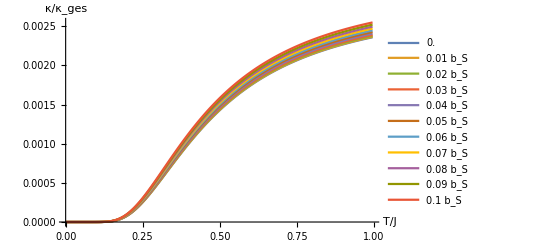

```mathematica
ListPlot[narrowedtopismallfield,PlotLegends->Table["b_S" N[i],{i,0,1,0.1/(Length[narrowedtopismallfield]-1)}],Joined->True,AxesLabel->{Style["T/J",18],Style["κ/κ_ges",18]},PlotRange->All]
```

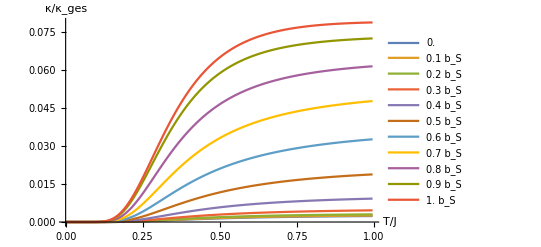

```mathematica
ListPlot[narrowedtopilargefield,PlotLegends->Table["b_S" N[i],{i,0,1,1/(Length[narrowedtopilargefield]-1)}],Joined->True,AxesLabel->{Style["T/J",18],Style["κ/κ_ges",18]},PlotRange->All]
```

center and edges

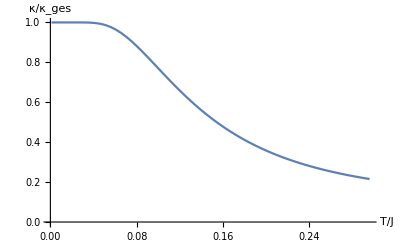

```mathematica
ListPlot[Table[{narrowedtocentersmallfield[[1]][[i]][[1]],narrowedtocentersmallfield[[1]][[i]][[2]]+narrowedtoedgessmallfield[[1]][[i]][[2]]},{i,1,Length[narrowedtocentersmallfield[[1]]]}],PlotRange->All,Joined->True,AxesLabel->{Style["T/J",18],Style["κ/κ_ges",18]},PlotRange->All]
```

## Thermal conductivity for constant temperature but different fields

```mathematica
blist=Table[{b,NIntegrate[heatconductivitydensity[kx,ky,b,1/0.3,1],{kx,-π,π},{ky,-π,π},MaxRecursion->100000,MinRecursion->90000,AccuracyGoal->100]},{b,0,1,0.01}];
```

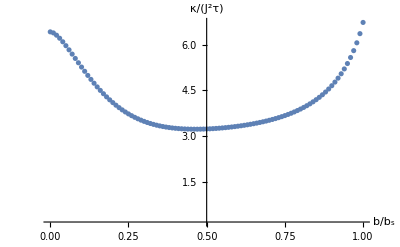

```mathematica
ListPlot[blist,PlotRange->All,AxesOrigin->{0.5,0.2},AxesLabel->{Style["b/b_s",18],Style["κ/(J^2τ)",18]}]
```

```mathematica
kappaB[[50]]
```

{0.245,0.11282,0.162159,0.220235,0.286957,0.362276,0.446212,0.538873,0.640434,0.751099,0.871052,1.0004,1.13913,1.28709,1.44396,1.60929,1.78247,1.96278,2.14941,2.34151,2.53817,2.73848,2.94156,3.14654,3.35261,3.55899,3.76499}

```mathematica
Length[kappaB[[1]]]
```

27

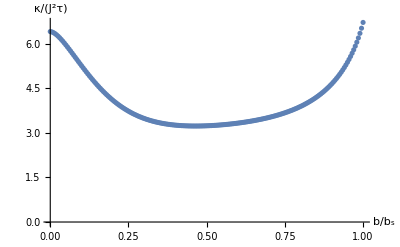

```mathematica
ListPlot[Table[{kappaB⟦i⟧⟦1⟧,kappaB⟦i⟧⟦27⟧},{i,1,Length[kappaB]}],PlotRange->All,AxesOrigin->{0.0,0.0},AxesLabel->{Style["b/b_s",18],Style["κ/(J^2τ)",18]}]
```

```mathematica
kappaB=ParallelTable[Flatten[{b,Table[NIntegrate[heatconductivitydensity[kx,ky,b,1/T,1],{kx,-π,π},{ky,-π,π},MaxRecursion->100000,MinRecursion->90000,AccuracyGoal->100],{T,0.05,0.5,0.05}]},1],{b,0.0,1.0,0.005}];
Export["/home/bkoehler/Documents/Wolfram Mathematica/Antiferromagnet/fancyplot/kappafulltauconstBdep.dat",kappaB,"Data"];
kappaBnormed=ParallelTable[Flatten[{b,Table[NIntegrate[heatconductivitydensity[kx,ky,b,1/T,1],{kx,-π,π},{ky,-π,π},MaxRecursion->100000,MinRecursion->90000,AccuracyGoal->100]/NIntegrate[heatconductivitydensity[kx,ky,0,1/T,1],{kx,-π,π},{ky,-π,π},MaxRecursion->100000,MinRecursion->90000,AccuracyGoal->100],{T,0.05,0.5,0.05}]},1],{b,0.0,1.0,0.005}];
Export["/home/bkoehler/Documents/Wolfram Mathematica/Antiferromagnet/fancyplot/kappafulltauconstBdepnormed.dat",kappaBnormed,"Data"];
```

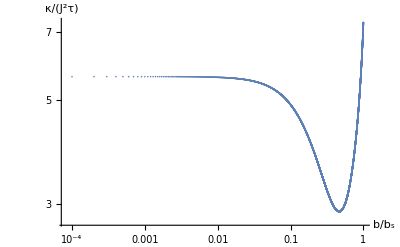

```mathematica
ListLogLogPlot[blist,PlotRange->All,AxesLabel->{Style["b/b_s",18],Style["κ/(J^2τ)",18]}]
```

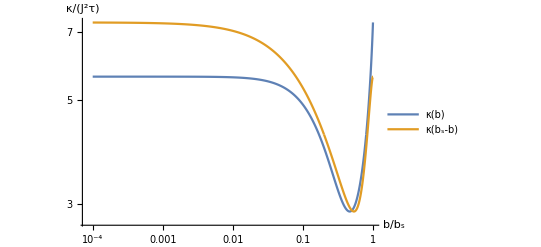

```mathematica
ListLogLogPlot[{blist,Table[{1-blist[[i]][[1]],blist[[i]][[2]]},{i,1,Length[blist]}]},PlotRange->All,AxesLabel->{Style["b/b_s",18],Style["κ/(J^2τ)",18]},PlotLegends->{"κ(b)","κ(b_s-b)"},Joined->True]
```

## asymptotic behaviour

entire Brillouin zone

```mathematica
list=Table[{Log[T],Log[NIntegrate[heatconductivitydensity[kx,ky,1,1/T,1],{kx,-π,π},{ky,-π,π},MaxRecursion->100000,MinRecursion->90000,AccuracyGoal->100]]},{T,1/1000,2/10,1/10000}];
```

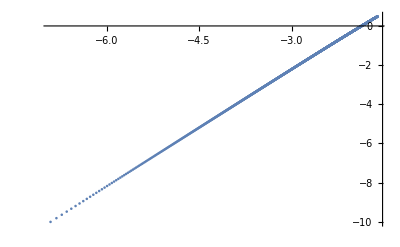

```mathematica
ListPlot[list,PlotRange->All]
```

```mathematica
Fit[list,{1,x},x]
```

3.68548+1.97031 x

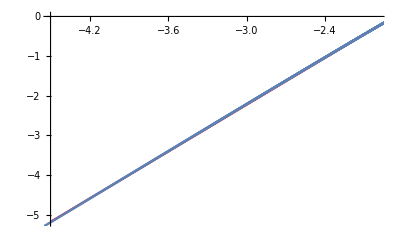

```mathematica
Show[Plot[3.685476587987679+1.9703135354971666 x,{x,-4.5,-2},PlotStyle->Red],ListPlot[list]]
```

just center of Brillouin zone

```mathematica
centerlist=Table[{Log[T],Log[NIntegrate[heatconductivitydensity[kx,ky,0.0001,1/T,1],{kx,-Δ,Δ},{ky,-Δ,Δ},MaxRecursion->100000,MinRecursion->90000,AccuracyGoal->100]]},{T,1/1000,0.6/10,1/10000}];
```

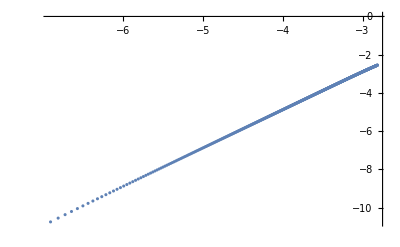

```mathematica
ListPlot[centerlist,PlotRange->All]
```

```mathematica
test=DeleteDuplicatesBy[centerlist,Last];
test=Drop[test,1];
```

```mathematica
Fit[test,{1,x},x]
```

3.0981+1.99616 x

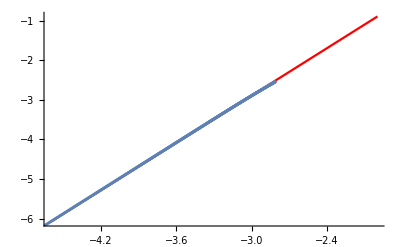

```mathematica
Show[Plot[3.0980994317465633+1.996157407885185 x,{x,-4.6,-2},PlotStyle->Red],ListPlot[test]]
```

## sophisticated lifetimes

```mathematica
J=1;
z=4;
γ[kx_,ky_]:=1/2*(Cos[kx]+Cos[ky]);
ϵ[kx_,ky_,b_]:=2*J*Sqrt[(1+γ[kx,ky])(1+γ[kx,ky]*(2*b^2-1))];
heatconductivitydensityempiric[kx_,ky_,b_,β_,ξ_]:=-(J^2 (-z/2*b^2-2*γ[kx,ky]*(2*b^2-1)))^2*(Sin[kx]^2+Sin[ky]^2)*(β^2/2)/(1-Cosh[β*ϵ[kx,ky,b]])*(1)/(ξ[##])&;
ξac[kx_,ky_,β_,b_]:=Sqrt[(kx-π)^2+(ky-π)^2]/(β^2*16*Sqrt[2]);
ξmm[kx_,ky_,β_,b_]:=Sqrt[kx^2+ky^2]*Exp[-2.2*J*β];
ξgb[kx_,ky_,β_,b_]:=J*Sqrt[2]/150;
ξcor[kx_,ky_,β_,b_]:=J*Sqrt[2]/(1.13*J*Exp[1.13*J*β]/(2.26*J+1/β));
ξcomb[kx_,ky_,β_,b_]:=J*Sqrt[2]/150+0.3*(Sqrt[(kx-π)^2+(ky-π)^2])^2/(β^2);
```

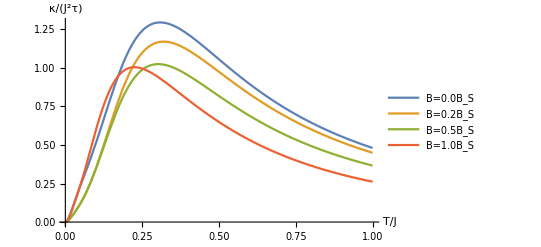

```mathematica
Plot[{1/(4π^2)*NIntegrate[heatconductivitydensityempiric[kx,ky,0,1/T,ξcomb][kx,ky,1/T,0],{kx,-π,π},{ky,-π,π},MaxRecursion->100000,MinRecursion->90000,AccuracyGoal->100],1/(4π^2)*NIntegrate[heatconductivitydensityempiric[kx,ky,0.2,1/T,ξcomb][kx,ky,1/T,0.2],{kx,-π,π},{ky,-π,π},MaxRecursion->100000,MinRecursion->90000,AccuracyGoal->100],1/(4π^2)*NIntegrate[heatconductivitydensityempiric[kx,ky,0.5,1/T,ξcomb][kx,ky,1/T,0.5],{kx,-π,π},{ky,-π,π},MaxRecursion->100000,MinRecursion->90000,AccuracyGoal->100],1/(4π^2)*NIntegrate[heatconductivitydensityempiric[kx,ky,1,1/T,ξcomb][kx,ky,1/T,1],{kx,-π,π},{ky,-π,π},MaxRecursion->100000,MinRecursion->90000,AccuracyGoal->100]},{T,0.001,1},AxesOrigin->{0,0},PlotRange->All,AxesLabel->{Style["T/J",18],Style["κ/(J^2τ)",18]},PlotLegends->{"B=0.0B_S","B=0.2B_S","B=0.5B_S","B=1.0B_S"}]
```

```mathematica
blistempiric=Table[Flatten[{T,Table[1/(4π^2)*NIntegrate[heatconductivitydensityempiric[kx,ky,b,1/T,ξcomb][kx,ky,1/T,b],{kx,-π,π},{ky,-π,π},MaxRecursion->100000,MinRecursion->90000,AccuracyGoal->100],{b,0,1,0.1}]},1],{T,0.001,3,0.0005}];
Export["/home/bkoehler/Documents/Wolfram Mathematica/Antiferromagnet/fancyplot/BfieldtauempTdep.dat",blistempiric,"Data"]
```

/home/bkoehler/Documents/Wolfram Mathematica/Antiferromagnet/fancyplot/BfieldtauempTdep.dat

```mathematica
Manipulate[DensityPlot[heatconductivitydensity[x,y,b,1/T,1],{x,-π,π},{y,-π,π},PlotRange->All],{b,0,1},{T,0.01,2}]
```

```mathematica
Manipulate[DensityPlot[heatconductivitydensityempiric[x,y,b,1/T,ξcomb][x,y,1/T,b],{x,-π,π},{y,-π,π},PlotRange->All,PlotLegends->Automatic],{b,0,1},{T,0.001,2}]
```

```mathematica
Manipulate[Plot[{heatconductivitydensityempiric[x,x,b,1/T,ξcomb][x,x,1/T,b]},{x,0,π},PlotRange->All],{T,0.001,1},{b,0.0,1}]
```

```mathematica
Manipulate[Plot[{heatconductivitydensity[x,x,b,1/T,1]},{x,0,π},PlotRange->All],{T,0.001,1},{b,0.0,1}]
```

```mathematica
Plot3D[1/(4π^2)*NIntegrate[heatconductivitydensityempiric[kx,ky,b,1/T,ξcomb][kx,ky,1/T,b],{kx,-π,π},{ky,-π,π},MaxRecursion->100000,MinRecursion->90000,AccuracyGoal->100],{T,0.001,1},{b,0,1},AxesOrigin->{0,0},PlotRange->All,AxesLabel->{Style["T/J",18],Style["B/B_S",18],Style["κ/(J^2τ)",18]},MeshFunctions->{#1&,#2&}]
```

-Graphics3D-

```mathematica
sophblist=ParallelTable[Table[{T,b,1/(4π^2)*NIntegrate[heatconductivitydensityempiric[kx,ky,b,1/T,ξcomb][kx,ky,1/T,b],{kx,-π,π},{ky,-π,π},MaxRecursion->100000,MinRecursion->90000,AccuracyGoal->100]},{T,0.001,1,0.001}],{b,Flatten[{Table[0.01*i,{i,0,100}]}]}];
```

```mathematica
ListPointPlot3D[sophblist,PlotRange->All,AxesLabel->{Style["T/J",18],Style["B/B_S",18],Style["κ/(J^2τ)",18]},Boxed->False,AxesOrigin->{0,0,0}]
```

-Graphics3D-

```mathematica
Export["fulldata.out",Table[Flatten[{sophblist⟦1⟧⟦i⟧⟦1⟧,Flatten[Table[{sophblist⟦j⟧⟦i⟧⟦2⟧,sophblist⟦j⟧⟦i⟧⟦3⟧},{j,1,Length[sophblist]}]]}],{i,1,Length[sophblist⟦1⟧]}],"Table"];
```

```mathematica
smallblist=ParallelTable[Table[{T,b,1/(4π^2)*NIntegrate[heatconductivitydensityempiric[kx,ky,b,1/T,ξcomb][kx,ky,1/T,b],{kx,-π,π},{ky,-π,π},MaxRecursion->100000,MinRecursion->90000,AccuracyGoal->100]},{T,0.001,1,0.001}],{b,Flatten[{Table[0.01*i,{i,0,20}]}]}];
largeblist=ParallelTable[Table[{T,b,1/(4π^2)*NIntegrate[heatconductivitydensityempiric[kx,ky,b,1/T,ξcomb][kx,ky,1/T,b],{kx,-π,π},{ky,-π,π},MaxRecursion->100000,MinRecursion->90000,AccuracyGoal->100]},{T,0.001,1,0.001}],{b,Flatten[{Table[0.90+0.01*i,{i,1,10}]}]}];
```

```mathematica
ListPointPlot3D[smallblist,PlotRange->All,AxesLabel->{Style["T/J",18],Style["B/B_S",18],Style["κ/(J^2τ)",18]},Boxed->False,AxesOrigin->{0,0,0}]
```

-Graphics3D-

```mathematica
smallblistsmallT=ParallelTable[Table[{T,0,1/(4π^2)*NIntegrate[heatconductivitydensityempiric[kx,ky,0,1/T,ξcomb][kx,ky,1/T,0],{kx,-π,π},{ky,-π,π},MaxRecursion->100000,MinRecursion->90000,AccuracyGoal->100]},{T,0.005,0.5,0.001}],{b,Flatten[{Table[0.01*i,{i,0,1}]}]}];
```

```mathematica
ListPointPlot3D[smallblistsmallT[[1]][[1;;50]]]
```

-Graphics3D-

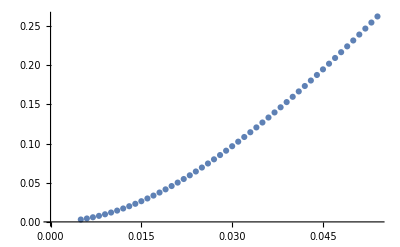

```mathematica
ListPlot[Table[{smallblistsmallT[[1]][[i]][[1]],smallblistsmallT[[1]][[i]][[3]]},{i,1,50}],AxesOrigin->{ 0,0}]
```

```mathematica
Export["smallbdata.out",Table[Flatten[{smallblist⟦1⟧⟦i⟧⟦1⟧,Flatten[Table[{smallblist⟦j⟧⟦i⟧⟦2⟧,smallblist⟦j⟧⟦i⟧⟦3⟧},{j,1,Length[smallblist]}]]}],{i,1,Length[smallblist⟦1⟧]}],"Table"];
```

```mathematica
ListPointPlot3D[largeblist,PlotRange->All,AxesLabel->{Style["T/J",18],Style["B/B_S",18],Style["κ/(J^2τ)",18]},Boxed->False,AxesOrigin->{0,1,0}]
```

-Graphics3D-

```mathematica
Export["largebdata.out",Table[Flatten[{largeblist⟦1⟧⟦i⟧⟦1⟧,Flatten[Table[{largeblist⟦j⟧⟦i⟧⟦2⟧,largeblist⟦j⟧⟦i⟧⟦3⟧},{j,1,Length[largeblist]}]]}],{i,1,Length[largeblist⟦1⟧]}],"Table"];
```

```mathematica
sophblistshort=ParallelTable[Table[{T,b,1/(4π^2)*NIntegrate[heatconductivitydensityempiric[kx,ky,b,1/T,ξcomb][kx,ky,1/T,b],{kx,-π,π},{ky,-π,π},MaxRecursion->100000,MinRecursion->90000,AccuracyGoal->100]},{T,0.1,0.4,0.001}],{b,Flatten[{Table[0.001*i,{i,0,1000}]}]}];
sortedlargetest=Table[Sort[sophblistshort[[i]],#1[[3]]>#2[[3]]&][[1]],{i,1,Length[sophblistshort]}];
```

```mathematica
Export["/home/bkoehler/Documents/Wolfram Mathematica/Antiferromagnet/fancyplot/Bfieldtauempmaximum.dat",sortedlargetest,"Data"]
```

/home/bkoehler/Documents/Wolfram Mathematica/Antiferromagnet/fancyplot/Bfieldtauempmaximum.dat

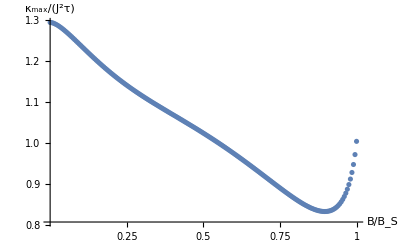

```mathematica
ListPlot[Table[{sortedlargetest[[i]][[2]],sortedlargetest[[i]][[3]]},{i,1Length[sortedlargetest]}],PlotRange->All,AxesLabel->{Style["B/B_S",18],Style["κ_max/(J^2τ)",18]},Ticks->{{0.25,0.5,0.75,1},Automatic}]
```

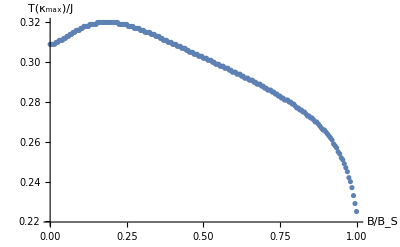

```mathematica
ListPlot[Table[{sortedlargetest[[i]][[2]],sortedlargetest[[i]][[1]]},{i,1Length[sortedlargetest]}],PlotRange->All,AxesLabel->{Style["B/B_S",18],Style["T(κ_max)/J",18]}]
```

```mathematica
listempiric=Table[{Log[T],Log[1/(4π^2)*NIntegrate[heatconductivitydensityempiric[kx,ky,1,1/T,ξcomb][kx,ky,1/T,1],{kx,-π,π},{ky,-π,π},MaxRecursion->100000,MinRecursion->90000,AccuracyGoal->100]]},{T,0.001,Exp[-4.1],0.00005}];
```

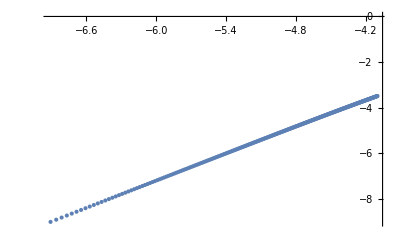

```mathematica
ListPlot[listempiric]
```

```mathematica
Fit[listempiric,{1,x},x]
```

4.60205+1.96625 x

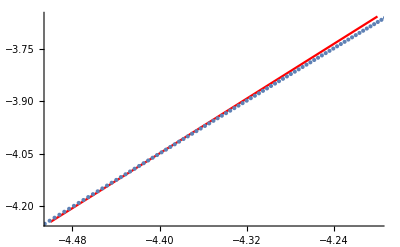

```mathematica
Show[Plot[4.602045503173347+1.9662508628644397 x,{x,-4.5,-4.2},PlotStyle->Red],ListPlot[listempiric]]
```

```mathematica
sorted=Sort[listempiric,#1[[2]]>#2[[2]]&];
counted=Count[Table[sorted[[i]][[2]],{i,1,Length[listempiric]}],listempiric[[1]][[2]]];
i=1;
While[i<=counted,
sorted=Delete[sorted,1];
i++;]
```

```mathematica
Fit[sorted,{1,x},x]
```

4.60291+1.96641 x

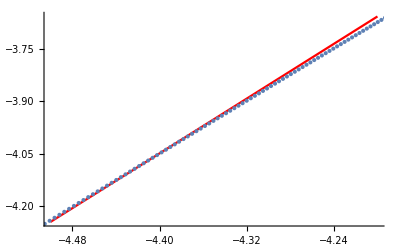

```mathematica
Show[Plot[4.602912742046261+1.9664087948136468 x,{x,-4.5,-4.2},PlotStyle->Red],ListPlot[sorted]]
```

## Thermal Conductivity for narrowed Brillouin zone with empiric lifetime

center

```mathematica
Δ=π/10;
narrowedtocentersmallfield=ParallelTable[Table[{T,NIntegrate[heatconductivitydensityempiric[kx,ky,b,1/T,ξcomb][kx,ky,1/T,b],{kx,-Δ,Δ},{ky,-Δ,Δ},MaxRecursion->100000,MinRecursion->90000,AccuracyGoal->100]/NIntegrate[heatconductivitydensityempiric[kx,ky,b,1/T,ξcomb][kx,ky,1/T,b],{kx,-π,π},{ky,-π,π},MaxRecursion->100000,MinRecursion->90000,AccuracyGoal->100]},{T,0.001,0.2,0.001}],{b,0,0.01,0.002}];
narrowedtocenterlargefield=ParallelTable[Table[{T,NIntegrate[heatconductivitydensityempiric[kx,ky,b,1/T,ξcomb][kx,ky,1/T,b],{kx,-Δ,Δ},{ky,-Δ,Δ},MaxRecursion->100000,MinRecursion->90000,AccuracyGoal->100]/NIntegrate[heatconductivitydensityempiric[kx,ky,b,1/T,ξcomb][kx,ky,1/T,b],{kx,-π,π},{ky,-π,π},MaxRecursion->100000,MinRecursion->90000,AccuracyGoal->100]},{T,0.001,0.3,0.001}],{b,0.9,1,0.01}];
```

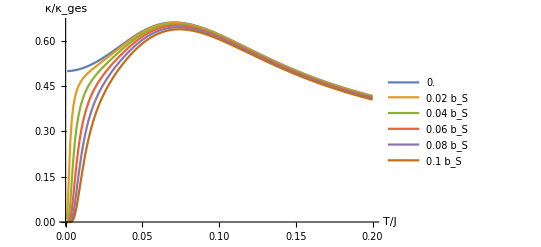

```mathematica
ListPlot[narrowedtocentersmallfield,PlotLegends->Table["b_S" N[0.1*i],{i,0,1,1/(Length[narrowedtocentersmallfield]-1)}],Joined->True,AxesLabel->{Style["T/J",18],Style["κ/κ_ges",18]}]
```

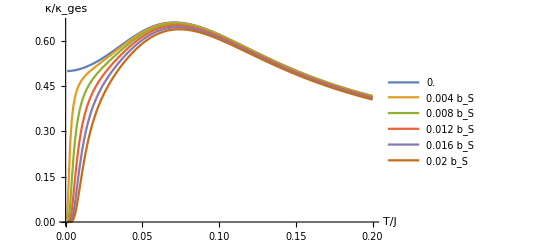

```mathematica
ListPlot[narrowedtocentersmallfield,PlotLegends->Table["b_S" N[0.1*i],{i,0,1,0.2/(Length[narrowedtocentersmallfield]-1)}],Joined->True,AxesLabel->{Style["T/J",18],Style["κ/κ_ges",18]}]
```

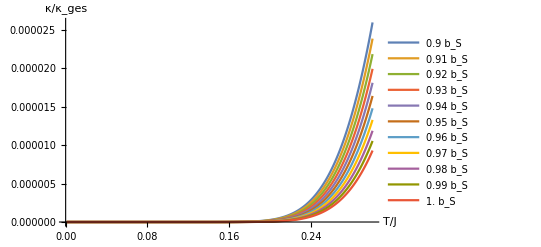

```mathematica
ListPlot[narrowedtocenterlargefield,PlotLegends->Table["b_S" N[i+0.9],{i,0,1,0.1/(Length[narrowedtocenterlargefield]-1)}],Joined->True,AxesLabel->{Style["T/J",18],Style["κ/κ_ges",18]},PlotRange->All]
```

edges

```mathematica
narrowedtoedgessmallfield=ParallelTable[Table[{T,4*NIntegrate[heatconductivitydensityempiric[kx,ky,b,1/T,ξcomb][kx,ky,1/T,b],{kx,-π,-π+Δ},{ky,-π,-π+Δ},MaxRecursion->100000,MinRecursion->90000,AccuracyGoal->100]/NIntegrate[heatconductivitydensityempiric[kx,ky,1,1/T,ξcomb][kx,ky,1/T,b],{kx,-π,π},{ky,-π,π},MaxRecursion->100000,MinRecursion->90000,AccuracyGoal->100]},{T,0.001,0.2,0.005}],{b,0,0.5,0.1}];
narrowedtoedgeslargefield=ParallelTable[Table[{T,4*NIntegrate[heatconductivitydensityempiric[kx,ky,b,1/T,ξcomb][kx,ky,1/T,b],{kx,-π,-π+Δ},{ky,-π,-π+Δ},MaxRecursion->100000,MinRecursion->90000,AccuracyGoal->100]/NIntegrate[heatconductivitydensityempiric[kx,ky,b,1/T,ξcomb][kx,ky,1/T,b],{kx,-π,π},{ky,-π,π},MaxRecursion->100000,MinRecursion->90000,AccuracyGoal->100]},{T,0.001,0.2,0.005}],{b,0.9,1,0.01}];
```

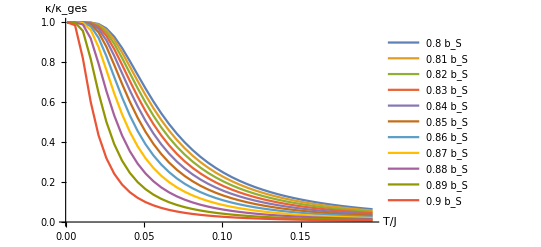

```mathematica
ListPlot[narrowedtoedgeslargefield,PlotLegends->Table["b_S" N[i+0.8],{i,0,1,0.1/(Length[narrowedtoedgeslargefield]-1)}],Joined->True,AxesLabel->{Style["T/J",18],Style["κ/κ_ges",18]},PlotRange->All]
```

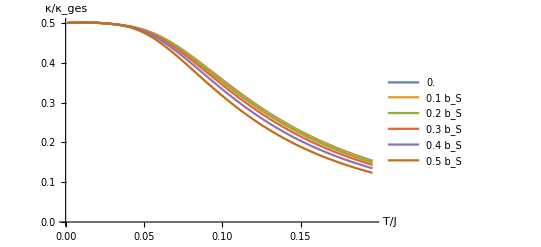

```mathematica
ListPlot[narrowedtoedgessmallfield,PlotLegends->Table["b_S" N[i],{i,0,1,1/(Length[narrowedtoedgeslargefield]-1)}],Joined->True,AxesLabel->{Style["T/J",18],Style["κ/κ_ges",18]},PlotRange->All]
```